```mathematica
Predicting Bitcoin Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

- Metcalfe's law.

## Resources

- Bitcoin hourly price: Recent (≥ 2024) data - bitstamp.com.

- Bitcoin circulating supply: https://www.blockchain.com/charts/total-bitcoins.

## In This Notebook

LPPLS model implementation (2026 ed.).

```mathematica
base=DirectoryName[NotebookFileName[]];
lastPriceDate=DateString[Yesterday,"ISODate"]
```

2026-01-30

```mathematica
hourlyPricesUrl="https://www.cryptodatadownload.com/cdd/Bitstamp_BTCUSD_1h.csv";
prices =Import[hourlyPricesUrl, HeaderLines->1]
```

```mathematica
(* First price date: *)
firstDownloadedDateTime=prices[[-1]][[2]];
{firstDownloadedDate,firstDownloadedTime}=StringSplit[firstDownloadedDateTime];
firstPriceDate=firstDownloadedDate
```

2018-05-15

```mathematica
(* Some freshness checks: *)
lastDownloadedDateTime=prices[[2]][[2]];
{lastDownloadedDate, lastDownloadedTime}=StringSplit[lastDownloadedDateTime]
{DateString[DatePlus[lastDownloadedDate, -1], "ISODate"]==lastPriceDate, lastDownloadedTime=="00:00:00"}
```

{2026-01-31,00:00:00}

{True,True}

```mathematica
closingPrices={#[[1]],#[[7]]}&/@prices
```

```mathematica
(* Filter non-numerical values *)
closingPricesFilter=Select[closingPrices, NumberQ[#[[2]]]&]
```

```mathematica
(* Hourly data *)
hourlyPrices=SortBy[closingPricesFilter, First]
```

```mathematica
Length[hourlyPrices]
```

67607

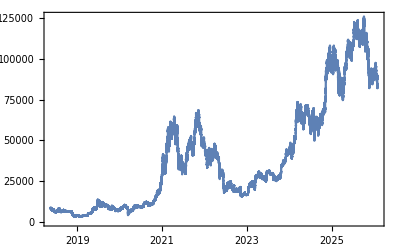

```mathematica
DateListPlot[hourlyPrices,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
Export[base<>"csv/Bitcoin_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv",hourlyPrices]
```

/Users/mauro/Projects/Bitcoin/csv/Bitcoin_price-hourly-20180515-20260130.csv

```mathematica
(* Convert to market capitalization, using circulating supply data, from blockchain.info *)
(* Load circulating supply data: https://www.blockchain.com/charts/total-bitcoins *)
supplyJsonData = Import["https://api.blockchain.info/charts/total-bitcoins?timespan=all&sampled=true&metadata=false&daysAverageString=1d&cors=true&format=json"];
```

```mathematica
supplyJson=supplyJsonData[[6]][[2]]
```

```mathematica
supplyTs=supplyJson[[All, 1]][[All,2]];
supplyQuantity=supplyJson[[All, 2]][[All,2]];
```

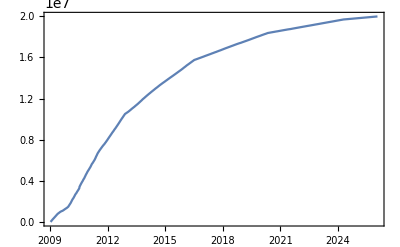

```mathematica
supplyTimestamps=MapThread[{#1, #2}&,{supplyTs, supplyQuantity}];
DateListPlot[supplyTimestamps,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Create an interpolating function from it *)
supplyFunction=Block[{},Off[ InterpolatingFunction::dmval];Interpolation[supplyTimestamps]]
```

InterpolatingFunction[…]

```mathematica
{supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}
```

{1231568277,1769436794}

```mathematica
{hourlyPrices[[1]][[1]],hourlyPrices[[-1]][[1]]}
```

{1526364000,1769817600}

```mathematica
{supplyFunction[hourlyPrices[[1]][[1]]], supplyFunction[hourlyPrices[[-3]][[1]]]}
```

{1.70341×10^7,1.99822×10^7}

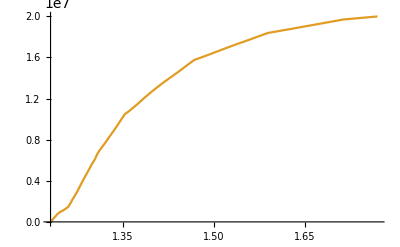

```mathematica
Plot[{,supplyFunction[i]}, {i, supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}]
```

```mathematica
(* Generate hourly market capitalization data *)
hourlyMarketCap={#[[1]], #[[2]]*supplyFunction[#[[1]]]}&/@hourlyPrices
```

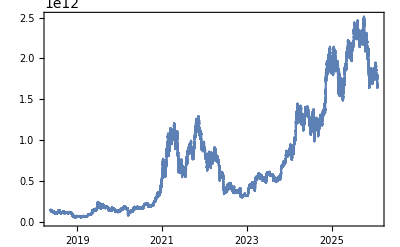

```mathematica
DateListPlot[hourlyMarketCap, DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Use the Log Market Cap *)
logMarketCap= {#[[1]], Log[#[[2]]]}&/@hourlyMarketCap
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2026 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2025-11-23", lastPriceDate}}
```

{{2025-11-23,2026-01-30}}

```mathematica
bubbleN=Length[bubblesDate]
```

1

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1763852400,1769727600}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{68}

```mathematica
bubbles=Table[Select[logMarketCap,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, bubbleN}];
#[[1]]&/@bubbles
```

{{1763852400,28.1555}}

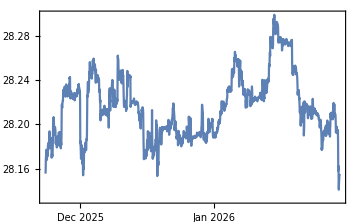

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{1.28605,0.0904445}}

```mathematica
Length/@bubblesScaled
```

{1633}

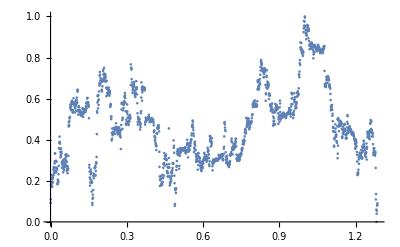

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
(* Export bubbles data: *)
bubbleScaledCsvs=MapIndexed[Export[base<>"csv/bubbleScaled-Bitcoin-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,bubblesScaled]
```

{/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Bitcoin-1.tsv}

```mathematica
(* Our "goodness of fit" control parameter. The smaller the better. i.e. stricter hypothesis testing will be. *)
(* Empirically, spans greater than 0.1 indicate that our prediction is not very reliable / trustworthy. *)bestSpan=0.09
```

0.09

```mathematica
(* Get params from R: *)
rInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@bubbleScaledCsvs;
```

```mathematica
rRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@rInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
rParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@rRuns
```

{{17.6372,1609.8}}

```mathematica
(* {RSS, SE, SE of the fit}: *)
rErrors=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-6;;;;2]]&/@rRuns
```

{{8.59668,0.0731003,0.00722834}}

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
bestFits = LoessR[#, Scaled[bestSpan], #[[All, 1]], {InterpolationOrder-> 1}]&/@bubblesScaled;
```

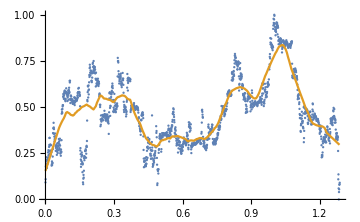

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, Scaled[bestSpan], t ]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, bubbleN}];
```

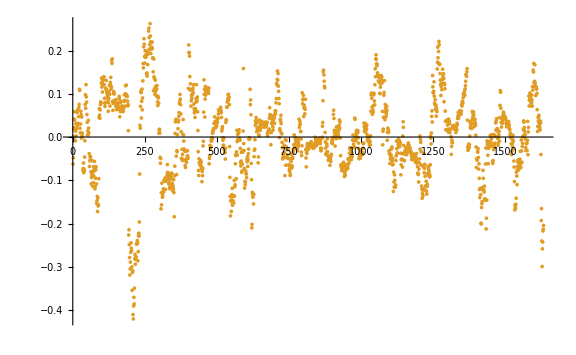

```mathematica
(* Plot residuals: *)
ListPlot[{{0,0},#}, ImageSize->Large]&/@ℛs
```

```mathematica
(* Standard deviations: *)
stdDevℛs=StandardDeviation /@ℛs
```

{0.092124}

```mathematica
(* Standardized residuals: *)
stdℛs = MapThread[#1/#2&,{ℛs, stdDevℛs}];
```

```mathematica
(* RSS: *)
ℛsSS =Total[#^2]&/@ℛs
```

{13.8585}

```mathematica
(* Larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[1]]]&,{ℛsSS,rErrors}]
```

{13.8585 > 8.59668}

```mathematica
(* Residual Standard Error(s): *)
ℛsSEs=MapThread[√(Total[#1^2]/(Length[#1]-#2[[1]]))&,{ℛs,rParams}]
```

{0.092624}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.092624 > 0.0731003}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(Length[#1]-#2[[1]]))&,{ℛs,rParams, rErrors}]
```

{0.0729509}

```mathematica
ℛsSEs=MapThread[√(Total[#1^2]/(#2[[2]]))&,{ℛs,rParams}]
```

{0.0927839}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0927839 > 0.0731003}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(#2[[2]]))&,{ℛs,rParams, rErrors}]
```

{0.0730768}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Select first bubble for fitting: *)
bubble=1
```

1

```mathematica
(* Use the selected bubble: *)
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Use the params for the selected bubble: *)
{estimatedNParams, effectiveDfs}=rParams[[bubble]]
```

{17.6372,1609.8}

```mathematica
(* Profiling over 0.1 < m < 1, 3 < ω < 14 and 1. < tc < 2 months in the future *)
minM=0.1;
maxM=1;
minω=3;
maxω=14;
months=2;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define `months` in the future scaled interval endpoint: *)
bubbleScaled[[-1]][[1]]
maxTc=bubbleScaled[[-1]][[1]]+(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.28605

3.1684

```mathematica
(* Define 3 days resolution scaled interval step: *)
stepTc=3/bubblesDays[[bubble]]//N
```

0.0441176

```mathematica
(* Define 3 days resolution scaled initial time step *)
stepTi=3/bubblesDays[[bubble]]//N
```

0.0441176

```mathematica
(* Slow. Shortcut below *)
Now[]
fits=Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[ParallelTable[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
RSS=Total[ℛ^2],
RSS/(Length[ℛ]-numParams),
StandardDeviation[ℛ],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10}, {ω,minω,maxω,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], RSS-> bestFit[[6]],ℛerror-> bestFit[[7]], ℛσ-> bestFit[[8]],LL-> bestFit[[9]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

Sat 31 Jan 2026 08:12:09GMT+1[]

{3223.83,{{a→4.29915,b→-3.6554,c→-0.0686864,d→-0.163773,T_1→0.,tc→2.34498,m→0.1,ω→14.,RSS→24.9113,ℛerror→0.0153206,ℛσ→0.123549,LL→3541.18,ρ→0.970853,σ→-0.0296026,μ→-6.79169×10^-17},{a→-1.83749,b→2.49151,c→-0.277185,d→-0.0363733,T_1→0.0441176,tc→1.46262,m→0.1,ω→3.,RSS→29.9277,ℛerror→0.0190622,ℛσ→0.137803,LL→3438.28,ρ→0.978906,σ→-0.0281457,μ→3.2808×10^-18},{a→-1.19529,b→1.78623,c→-0.24383,d→-0.0448127,T_1→0.0882353,tc→1.55086,m→0.1,ω→4.2,RSS→24.208,ℛerror→0.0159894,ℛσ→0.126199,LL→3325.85,ρ→0.976298,σ→-0.0273047,μ→-4.78678×10^-18},{a→-1.44116,b→2.0253,c→-0.236434,d→-0.0906851,T_1→0.132353,tc→1.59498,m→0.1,ω→4.5,RSS→23.9331,ℛerror→0.016415,ℛσ→0.127858,LL→3195.16,ρ→0.976681,σ→-0.0274413,μ→-1.18203×10^-17},{a→-1.33799,b→2.01127,c→-0.261297,d→0.0830716,T_1→0.176471,tc→1.4185,m→0.1,ω→3.1,RSS→22.0735,ℛerror→0.0157443,ℛσ→0.125209,LL→3105.81,ρ→0.975185,σ→-0.0277102,μ→-1.13554×10^-17},{a→-2.73813,b→3.20298,c→0.247132,d→-0.0878767,T_1→0.220588,tc→1.99203,m→0.1,ω→7.5,RSS→16.1669,ℛerror→0.012011,ℛσ→0.109351,LL→3013.1,ρ→0.970739,σ→-0.0262496,μ→-1.3707×10^-17},{a→-1.86395,b→2.42231,c→-0.159461,d→-0.213877,T_1→0.264706,tc→1.72733,m→0.1,ω→5.8,RSS→15.6212,ℛerror→0.0121095,ℛσ→0.109788,LL→2885.47,ρ→0.970423,σ→-0.0264938,μ→8.00172×10^-17},{a→-5.39423,b→5.6472,c→-0.283601,d→0.0214016,T_1→0.308824,tc→2.38909,m→0.1,ω→10.2,RSS→14.2415,ℛerror→0.0115409,ℛσ→0.107168,LL→2773.05,ρ→0.969975,σ→-0.0260532,μ→7.27098×10^-17},{a→-8.9621,b→8.86556,c→0.305,d→-0.0172115,T_1→0.352941,tc→2.74203,m→0.1,ω→11.8,RSS→13.8248,ℛerror→0.0117358,ℛσ→0.108057,LL→2664.25,ρ→0.971422,σ→-0.0256376,μ→7.3495×10^-17},{a→-2.47508,b→1.28793,c→0.028869,d→0.241534,T_1→0.397059,tc→3.13909,m→1.,ω→11.,RSS→13.4623,ℛerror→0.0119985,ℛσ→0.109246,LL→2551.85,ρ→0.972427,σ→-0.0254659,μ→3.13048×10^-17},{a→-2.95685,b→3.45723,c→-0.0232844,d→-0.31339,T_1→0.441176,tc→1.77145,m→0.1,ω→4.9,RSS→12.9157,ℛerror→0.012116,ℛσ→0.109764,LL→2424.86,ρ→0.972736,σ→-0.0254443,μ→-1.55459×10^-17},{a→-2.04421,b→1.30938,c→-0.213107,d→0.0244812,T_1→0.485294,tc→3.13909,m→0.8,ω→12.9,RSS→12.1452,ℛerror→0.0120249,ℛσ→0.109334,LL→2348.84,ρ→0.97529,σ→-0.0241433,μ→-3.04896×10^-17},{a→-1.37232,b→0.827549,c→-0.124504,d→-0.112019,T_1→0.529412,tc→3.13909,m→1.,ω→14.,RSS→11.3887,ℛerror→0.0119378,ℛσ→0.108918,LL→2240.15,ρ→0.976145,σ→-0.0236362,μ→1.03052×10^-17}}}

```mathematica
(* Shortcut: *)
fits=;
```

```mathematica
(* Timing in minutes: *)
fits[[1]]/60
```

53.7306

```mathematica
fits=fits[[2]];
```

```mathematica
fits[[All,{5,6,11,12}]]//TableForm
```

T_1→0. | tc→2.34498 | ℛσ→0.123549 | LL→3541.18
T_1→0.0441176 | tc→1.46262 | ℛσ→0.137803 | LL→3438.28
T_1→0.0882353 | tc→1.55086 | ℛσ→0.126199 | LL→3325.85
T_1→0.132353 | tc→1.59498 | ℛσ→0.127858 | LL→3195.16
T_1→0.176471 | tc→1.4185 | ℛσ→0.125209 | LL→3105.81
T_1→0.220588 | tc→1.99203 | ℛσ→0.109351 | LL→3013.1
T_1→0.264706 | tc→1.72733 | ℛσ→0.109788 | LL→2885.47
T_1→0.308824 | tc→2.38909 | ℛσ→0.107168 | LL→2773.05
T_1→0.352941 | tc→2.74203 | ℛσ→0.108057 | LL→2664.25
T_1→0.397059 | tc→3.13909 | ℛσ→0.109246 | LL→2551.85
T_1→0.441176 | tc→1.77145 | ℛσ→0.109764 | LL→2424.86
T_1→0.485294 | tc→3.13909 | ℛσ→0.109334 | LL→2348.84
T_1→0.529412 | tc→3.13909 | ℛσ→0.108918 | LL→2240.15

```mathematica
(* Average tc: *)
meanTc=Total[fits[[All,6]][[All,2]]]/Length[fits]
```

2.18547

```mathematica
minTc=Min[fits[[All,6]][[All,2]]]
maxTc=Max[fits[[All,6]][[All,2]]]
```

1.4185

3.13909

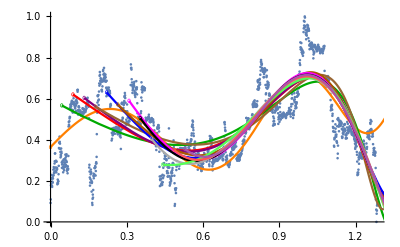

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black, Lighter[Gray], Lighter[Green], Lighter[Red], Lighter[Purple], Lighter[Brown], Lighter[Blue],Lighter[Orange]};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[i+1]]],""], {i,0,Length[fits]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* 4. Rejection criteria: See if the residuals errors of the fits (ℛerror field) are below the 95% of the simulated (standardized) RSSs: *)
T1s=Subscript[T, 1]/.fits
ℛerrors=ℛerror/.fits
RSSs=RSS/.fits
ℛσs=ℛσ/.fits
```

{0.,0.0441176,0.0882353,0.132353,0.176471,0.220588,0.264706,0.308824,0.352941,0.397059,0.441176,0.485294,0.529412}

{0.0153206,0.0190622,0.0159894,0.016415,0.0157443,0.012011,0.0121095,0.0115409,0.0117358,0.0119985,0.012116,0.0120249,0.0119378}

{24.9113,29.9277,24.208,23.9331,22.0735,16.1669,15.6212,14.2415,13.8248,13.4623,12.9157,12.1452,11.3887}

{0.123549,0.137803,0.126199,0.127858,0.125209,0.109351,0.109788,0.107168,0.108057,0.109246,0.109764,0.109334,0.108918}

```mathematica
(* Only last bubble *)
npBestFit=bestFits[[bubble]];
```

```mathematica
nPℓ=Length[npBestFit];
nPℓ
```

1633

```mathematica
(* Plot of the residuals of the non-parametric fit vs the residuals of the parametric fit: *)
(* Non-parametric residuals: *)
npℛs=ℛs[[bubble]];
```

```mathematica
(* Parametric residuals: *)
fullFit[t_]:=lpplsModel/.fits[[1]]/.ti-> t
pℛs=Table[bubbleScaled[[i]][[2]]-fullFit[bubbleScaled[[i]][[1]]],{i,1,Length[bubbleScaled]}];
```

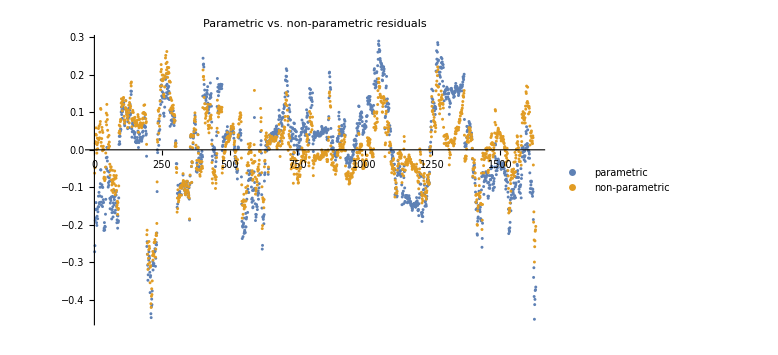

```mathematica
ListPlot[{pℛs,npℛs}, ImageSize->Large, {PlotLabel-> "Parametric vs. non-parametric residuals", PlotLegends->{"parametric","non-parametric"}}]
```

```mathematica
(* RSSs: *)
Total[#^2]&/@{npℛs, pℛs}
```

{13.8585,24.9113}

```mathematica
(* Residual Standard Errors: *)
{√(Total[npℛs^2]/effectiveDfs),√(Total[pℛs^2]/(Length[pℛs]-numParams)) }
```

{0.0927839,0.123776}

```mathematica
(* Mean residual squared error: *)
{Total[npℛs^2]/effectiveDfs,Total[pℛs^2]/(Length[pℛs]-numParams) }
```

{0.00860884,0.0153206}

```mathematica
selN=Length[T1s];
selN
```

13

```mathematica
selNpBestFit=Table[npBestFit[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selNpBestFit
```

{1633,1561,1489,1417,1345,1273,1201,1129,1057,985,913,841,769}

```mathematica
selBubbleScaled2=Table[bubbleScaled[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selBubbleScaled2
```

{1633,1561,1489,1417,1345,1273,1201,1129,1057,985,913,841,769}

```mathematica
(* Export selected bubbles: *)
selBubbleScaledCsvs=MapIndexed[Export[base<>"csv/selBubbleScaled-Bitcoin-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,selBubbleScaled2];
```

```mathematica
selBubbleScaled=#[[All,2]]&/@selBubbleScaled2;
```

```mathematica
selNpℛs=Table[selBubbleScaled[[i]]-selNpBestFit[[i]], {i, 1,selN}];
```

```mathematica
(* Structural checks: *)
Length/@selNpℛs
```

{1633,1561,1489,1417,1345,1273,1201,1129,1057,985,913,841,769}

```mathematica
selBubbleScaled[[1]][[1]]==bubbleScaled[[1]][[2]]
selNpBestFit[[1]][[1]]==npBestFit[[1]]
selNpℛs[[1]][[1]]==ℛs[[bubble]][[1]]
```

True

True

True

```mathematica
(* Magnitude of the parametric residual fits: *)
ℛerrors
```

{0.0153206,0.0190622,0.0159894,0.016415,0.0157443,0.012011,0.0121095,0.0115409,0.0117358,0.0119985,0.012116,0.0120249,0.0119378}

```mathematica
RSSs
```

{24.9113,29.9277,24.208,23.9331,22.0735,16.1669,15.6212,14.2415,13.8248,13.4623,12.9157,12.1452,11.3887}

```mathematica
(* For each selection, do the simulations, and compute all the statistics: *)
(* Standard deviations: *)
selStdDevℛs=StandardDeviation[#]& /@selNpℛs
```

{0.092124,0.0933414,0.0924896,0.084748,0.0749484,0.0732672,0.0726341,0.0729794,0.0720845,0.0717319,0.0728351,0.0749137,0.0774707}

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
selEstimatedAR1Models=FindProcessParameters[#,ar1Process]&/@selNpℛs
```

{{ρ→0.953433,σ→-0.0277766,μ→0.000103242},{ρ→0.954927,σ→-0.0276986,μ→0.000103518},{ρ→0.954524,σ→-0.027565,μ→3.0712×10^-6},{ρ→0.943996,σ→-0.0279534,μ→0.00013508},{ρ→0.935212,σ→-0.0265285,μ→-0.0000859938},{ρ→0.933772,σ→-0.0262097,μ→0.000140618},{ρ→0.934002,σ→-0.0259389,μ→-0.0000238337},{ρ→0.935953,σ→-0.0256864,μ→-0.0000882395},{ρ→0.934821,σ→-0.0255865,μ→-4.37739×10^-6},{ρ→0.942849,σ→-0.0238903,μ→0.000143692},{ρ→0.942529,σ→-0.0243227,μ→-0.0000423426},{ρ→0.943838,σ→-0.0247374,μ→0.0000770519},{ρ→0.946794,σ→-0.0249169,μ→0.0000982417}}

```mathematica
(* Compute the log-likelihood of the fit *)
selEstimatedProcesses=ar1Process/.#&/@selEstimatedAR1Models
logLikelihoods=Table[LogLikelihood[selEstimatedProcesses[[i]],selNpℛs[[i]]], {i, Length[T1s]}]
```

{ARProcess[0.000103242,{0.953433},0.000771541],ARProcess[0.000103518,{0.954927},0.000767212],ARProcess[3.0712×10^-6,{0.954524},0.00075983],ARProcess[0.00013508,{0.943996},0.00078139],ARProcess[-0.0000859938,{0.935212},0.000703761],ARProcess[0.000140618,{0.933772},0.000686947],ARProcess[-0.0000238337,{0.934002},0.000672829],ARProcess[-0.0000882395,{0.935953},0.000659793],ARProcess[-4.37739×10^-6,{0.934821},0.00065467],ARProcess[0.000143692,{0.942849},0.000570748],ARProcess[-0.0000423426,{0.942529},0.000591596],ARProcess[0.0000770519,{0.943838},0.000611941],ARProcess[0.0000982417,{0.946794},0.000620852]}

{3561.19,3412.59,3262.58,3131.64,3003.75,2856.2,2710.06,2560.43,2401.79,2313.2,2128.59,1948.51,1777.68}

```mathematica
(* Step 2: Characterize error variance. *)
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
selNPointss=Length/@selNpℛs;
nSims=1000;
selSims=ParallelTable[RandomFunction[selEstimatedProcesses[[i]],{0,selNPointss[[i]]-1},nSims], {i,selN}];
selNpℛsPlots=ParallelTable[MapThread[{#1,#2}&,{Range[0,selNPointss[[i]]-1],selNpℛs[[i]][[;;selNPointss[[i]]]]}], {i,selN}];
selPaths=#["Paths"]&/@selSims;
```

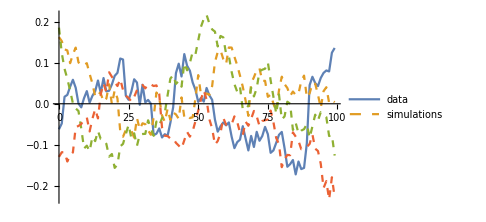
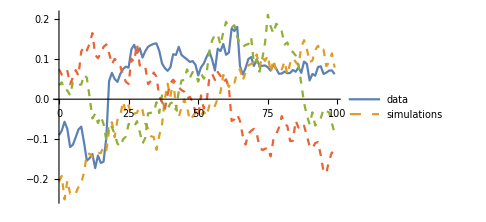
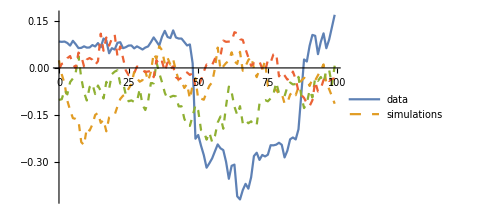
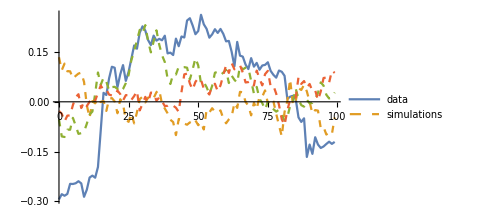
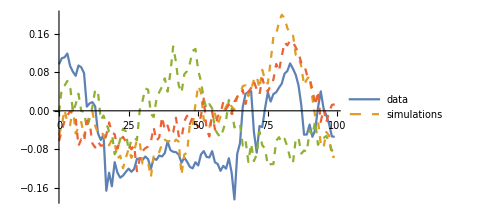
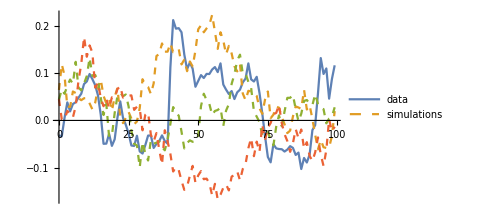
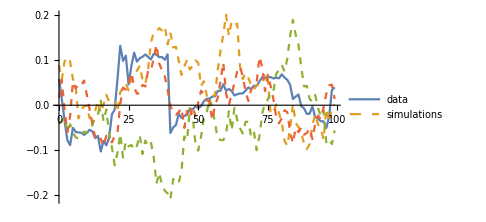
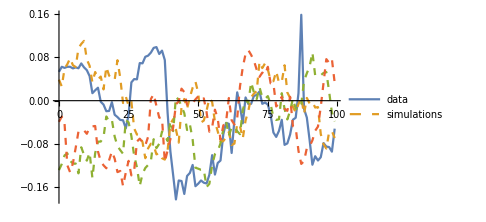

```mathematica
(* Show some simulations and data points *)
showSims=3;
showPoints=100;
Table[ListLinePlot[Join[{selNpℛsPlots[[i]][[;;showPoints]]}, selPaths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,selN}]
```

```mathematica
(* The estimated number of parameters of the sample selections fits: *)
(* From R's loess, using list of (selections) effective dfs: *)
selRInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@selBubbleScaledCsvs;
```

```mathematica
selRRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@selRInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
selRParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@selRRuns
```

{{17.6372,1609.8},{17.5835,1537.87},{17.5208,1465.96},{17.7292,1393.68},{17.6661,1321.77},{17.6122,1249.84},{17.5365,1177.94},{17.8006,1105.6},{17.7252,1033.7},{17.659,961.783},{17.5619,889.911},{17.9202,817.444},{17.8248,745.571}}

```mathematica
effectiveDfs
estimatedNParams
(*selEstimatedDfs=Table[Length[selBubbleScaled[[i]]]-estimatedNParams, {i, selN}]*)
selEffectiveDfs=Table[selRParams[[i]][[2]], {i, selN}]
```

1609.8

17.6372

{1609.8,1537.87,1465.96,1393.68,1321.77,1249.84,1177.94,1105.6,1033.7,961.783,889.911,817.444,745.571}

```mathematica
(* The "mean" RSSs (RSS/df) of the simulations: *)
selMeanRSSs=Table[Map[Total[(#[[All,2]])^2]/selEffectiveDfs[[i]]&,selPaths[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selMeanRSSs*)
```

```mathematica
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^3.," GB"}];
Needs["Utilities`CleanSlate`"]
memory
```

Memory Used: 1.75877 GB

```mathematica
Remove[selSims]
Remove[selNpℛsPlots]
memory
```

Memory Used: 1.75886 GB

```mathematica
CleanSlate[];
memory
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 248873 Kb

Memory Used: 1.52164 GB

```mathematica
(* The standardized "mean" RSSs: *)
selStdMeanRSSs=Table[Map[#/selStdDevℛs[[i]]&,selMeanRSSs[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selStdMeanRSSs*)
```

```mathematica
(* Count *)
selCounts=Table[With[{ℛerror= ℛerrors[[i]]},Select[selMeanRSSs[[i]],#>ℛerror &]//Length],{i,selN}]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
selPValues=Table[selCounts[[i]]/Length[selMeanRSSs[[i]]], {i, selN}]//N
```

{0.001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
selRejected=#<(1-0.95)&/@selPValues
```

{True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(* Take the first / largest interval that is not rejected *)
firstNotRejectedIndex=Select[Table[{i,selRejected[[i]]==False},{i,selN}], #[[2]]&]//First//#[[1]]&
```

First::nofirst: {} has zero length and no first element.

{}

```mathematica
(* As a fallback (if all rejected), take the one with the highest non-zero p-value *)
highestPRejected=ReverseSortBy[Select[MapIndexed[{#1, #2[[1]]}&, selPValues], 0< #[[1]]<(1-0.95)&], {#[[1]],-#[[2]]}&];
highestPRejectedIndex=If[Length[highestPRejected]>0, First[highestPRejected][[2]],{}]
```

1

```mathematica
(* As a fallback (if all rejected, and no positive p-values), take the one with the min tc *)
minTc=Min[fits[[;;,6,2]]]
minTcIndex=Select[Table[{i,fits[[i,6,2]]==minTc},{i,selN}],#[[2]]&]//First//#[[1]]&
```

1.4185

5

```mathematica
index=If[NumericQ[firstNotRejectedIndex], firstNotRejectedIndex,If[NumericQ[highestPRejectedIndex], highestPRejectedIndex, minTcIndex]]
```

1

```mathematica
selFit={fits[[index]], "index"-> index}//Flatten
```

{a→4.29915,b→-3.6554,c→-0.0686864,d→-0.163773,T_1→0.,tc→2.34498,m→0.1,ω→14.,RSS→24.9113,ℛerror→0.0153206,ℛσ→0.123549,LL→3541.18,ρ→0.970853,σ→-0.0296026,μ→-6.79169×10^-17,index→1}

```mathematica
bestIndex=index
fit=fits[[bestIndex]]
```

1

{a→4.29915,b→-3.6554,c→-0.0686864,d→-0.163773,T_1→0.,tc→2.34498,m→0.1,ω→14.,RSS→24.9113,ℛerror→0.0153206,ℛσ→0.123549,LL→3541.18,ρ→0.970853,σ→-0.0296026,μ→-6.79169×10^-17}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* Do it over the best params *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

0.1

14.

2.34498

3541.18

```mathematica
t1=Subscript[T, 1]/.fit
```

0.

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&];
```

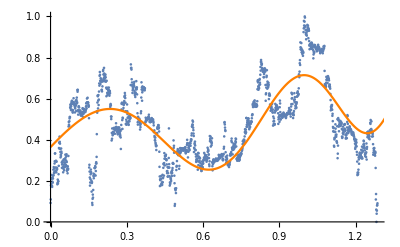

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→4.29915,b→-3.6554,c→-0.0686864,d→-0.163773,T_1→0.,tc→2.34498,m→0.1,ω→14.,RSS→24.9113,ℛerror→0.0153206,ℛσ→0.123549,LL→3541.18,ρ→0.970853,σ→-0.0296026,μ→-6.79169×10^-17}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest];
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.970853,σ→-0.0296026,μ→-6.79169×10^-17}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals until the LL is 1.92 times below the max: *)
lowCItc=bestTc;
lowCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/1000;
oldSign=1;
Monitor[While[delta=bestLL-lowCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
lowCItc=lowCItc+ precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],{delta}]
delta
{lowCItc, bestTc}
```

1.92007

{2.31683,2.34498}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc;
highCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/100;
oldSign=-1;
Monitor[While[delta=bestLL-highCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
highCItc=highCItc- precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],delta]
delta
{lowCItc, bestTc, highCItc}
```

1.92008

{2.31683,2.34498,2.39346}

```mathematica
(* Dates correction: *)
lastScaledTc=bubbleBest[[-1]][[1]]
```

1.28605

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc/lastScaledTc]
```

Wed 25 Mar 2026 12:03:12

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc/lastScaledTc]
```

Thu 26 Mar 2026 23:46:26

```mathematica
(* And the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc/lastScaledTc]
```

Sun 29 Mar 2026 13:18:22

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc/lastScaledTc]
```

Wed 18 Mar 2026 13:21:56

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc/lastScaledTc]
```

Thu 7 May 2026 23:30:33

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc/lastScaledTc]
```

Fri 6 Feb 2026 00:04:58

```mathematica
(* For reference: *)
{#[[5]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[5]][[2]]/lastScaledTc],#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]/lastScaledTc]}&/@fits//TableForm
```

T_1→0. | Sun 23 Nov 2025 00:00:00 | tc→2.34498 | Thu 26 Mar 2026 23:46:26
T_1→0.0441176 | Tue 25 Nov 2025 07:59:07 | tc→1.46262 | Sun 8 Feb 2026 08:04:05
T_1→0.0882353 | Thu 27 Nov 2025 15:58:14 | tc→1.55086 | Fri 13 Feb 2026 00:02:19
T_1→0.132353 | Sat 29 Nov 2025 23:57:21 | tc→1.59498 | Sun 15 Feb 2026 08:01:26
T_1→0.176471 | Tue 2 Dec 2025 07:56:28 | tc→1.4185 | Fri 6 Feb 2026 00:04:58
T_1→0.220588 | Thu 4 Dec 2025 15:55:35 | tc→1.99203 | Sun 8 Mar 2026 07:53:29
T_1→0.264706 | Sat 6 Dec 2025 23:54:42 | tc→1.72733 | Sun 22 Feb 2026 07:58:47
T_1→0.308824 | Tue 9 Dec 2025 07:53:49 | tc→2.38909 | Sun 29 Mar 2026 07:45:33
T_1→0.352941 | Thu 11 Dec 2025 15:52:56 | tc→2.74203 | Thu 16 Apr 2026 23:38:29
T_1→0.397059 | Sat 13 Dec 2025 23:52:03 | tc→3.13909 | Thu 7 May 2026 23:30:33
T_1→0.441176 | Tue 16 Dec 2025 07:51:10 | tc→1.77145 | Tue 24 Feb 2026 15:57:54
T_1→0.485294 | Thu 18 Dec 2025 15:50:17 | tc→3.13909 | Thu 7 May 2026 23:30:33
T_1→0.529412 | Sat 20 Dec 2025 23:49:24 | tc→3.13909 | Thu 7 May 2026 23:30:33

```mathematica
(* Compute market cap at the low leg of the best Tc: *)
bestM=bestLppls[bestTc-epsilon,bestTc]
```

2.86192

```mathematica
lowCIM=bestLppls[lowCItc,bestTc]
```

1.66323

```mathematica
lastScaledM=bubbleBest[[-1]][[2]]
Exp[lastScaledM]
```

0.0904445

1.09466

```mathematica
lastPriceDate
```

2026-01-30

```mathematica
(* Closing market cap at lastPriceDate date (`$lastPriceDate`) (https://coinmarketcap.com/currencies/bitcoin/historical-data/https://coinmarketcap.com/currencies/bitcoin/historical-data/Nonehttps://coinmarketcap.com/currencies/bitcoin/historical-data/HyperlinkActionRecycledHyperlinkActive) (Millions of USD): *)
(* Automated download *)
timeStartTs=UnixTime[lastPriceDate];
timeEndTs=timeStartTs+86400;
latestMarketCapUrl="https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart="<>ToString[timeStartTs]<>"&timeEnd="<>ToString[timeEndTs]<>"&interval=1d"
```

https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart=1769727600&timeEnd=1769814000&interval=1d

```mathematica
latestMarketCapData=Import[latestMarketCapUrl]
```

```mathematica
latestMarketCapInner=Flatten[latestMarketCapData[[1]][[2]][[5]][[2]]]
```

```mathematica
(* Build a list of timeCloses and marketCaps: *)
latestMarketCapWithTime=SortBy[MapThread[{#1, #2[[2]][[7]]}&,{latestMarketCapInner[[2;;-1;;5]], latestMarketCapInner[[5;;-1;;5]]}], First][[-1]]
```

{timeClose→2026-01-30T23:59:59.999Z,marketCap→1.68105564620842×10^12}

```mathematica
latestMarketCap=latestMarketCapWithTime[[2]][[2]]/10^7
```

168105.564620842

```mathematica
(* Plot predicted market cap evolution (USD) :*)
fixDate[brokenDate_]:= StringTake[brokenDate,2]<>"/"<>StringTake[brokenDate,3;;]
ticksH[min_,max_]:=Table[{i,Rotate[fixDate[Block[{$DateStringFormat={"Day","Month","/","YearShort"}},DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]i/lastScaledTc]]], π/3]},{i,{t1,lastScaledTc,lowCItc, bestTc, highCItc}}]
```

```mathematica
ticksVM[min_,max_]:=Table[{i,"$ "<>ToString[IntegerPart[i latestMarketCap/Exp[lastScaledM]]]<>"M"},{i,min, max,100}]
```

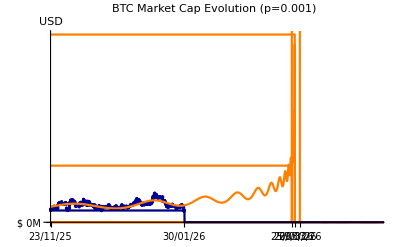

```mathematica
marketCapPrediction=Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Market Cap Evolution (p="<>ToString[selPValues[[index]]]<>")",PlotRange->{{0,maxTc},{0,Exp[bestM]}}, Ticks->{ticksH,ticksVM},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[Exp[lpplsModel/.fit]],UnitStep[ti-lowCItc]Exp[bestM+1],UnitStep[ti-highCItc]Exp[bestM+1]/.fit, UnitStep[lowCItc-ti]Exp[lowCIM],UnitStep[bestTc-ti]Exp[bestM],UnitStep[lastScaledTc-ti]Exp[lastScaledM]}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/BTC_MarketCapPrediction-"<>lastPriceDate<>".png",marketCapPrediction]
```

/Users/mauro/Projects/Bitcoin/png/BTC_MarketCapPrediction-2026-01-30.png

```mathematica
mToMarketCap[m_]:= latestMarketCap/Exp[lastScaledM] Exp[m]
```

```mathematica
lowCIMarketCap=mToMarketCap[lowCIM]
```

810280.

```mathematica
bestMarketCap=mToMarketCap[bestM]
```

2.68671×10^6

```mathematica
(* The price is the ratio of the market cap (in Millions USD) to the (predicted) supply at the date: *)
mToPrice[m_, date_]:=mToMarketCap[m]10^7/supplyFunction[UnixTime[date]]
```

```mathematica
tcToDate[tc_]:= DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]tc/lastScaledTc]
tcToDate[lastScaledTc]
```

Fri 30 Jan 2026 00:00:00

```mathematica
(* Check: *)
lastPrice=mToPrice[lastScaledM,tcToDate[lastScaledTc]]
```

84128.8

```mathematica
lowCIPrice=mToPrice[lowCIM, tcToDate[lowCItc]]//N
```

405968.

```mathematica
bestPrice=mToPrice[bestM, tcToDate[bestTc]]
```

1.34626×10^6

```mathematica
(* Plot predicted price evolution (USD) :*)
ticksVPrice[min_,max_]:=Table[{i,"$"<>ToString[IntegerPart[i/1000]]<>"K"},{i,min, max,IntegerPart[max/100000]10000}]
```

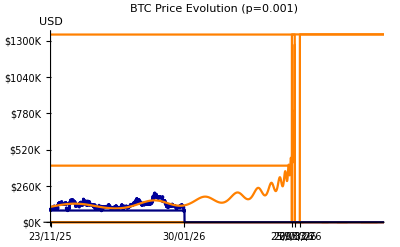

```mathematica
pricePrediction=Show[ListPlot[{#[[1]], mToPrice[#[[2]], tcToDate[#[[1]]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Price Evolution (p="<>ToString[selPValues[[index]]]<>")",PlotRange->{{0,maxTc},{0,bestPrice}}, Ticks->{ticksH,ticksVPrice},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[mToPrice[lpplsModel/.fit, tcToDate[ti]]],UnitStep[ti-lowCItc](bestPrice+1000),UnitStep[ti-highCItc](bestPrice+1000)/.fit, UnitStep[lowCItc-ti]lowCIPrice,UnitStep[bestTc-ti]bestPrice,UnitStep[lastScaledTc-ti]lastPrice}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/BTC_PricePrediction-"<>lastPriceDate<>".png",pricePrediction]
```

/Users/mauro/Projects/Bitcoin/png/BTC_PricePrediction-2026-01-30.png